```mathematica
(*   Constants   *)
fm2MeV = 1./197(*Conversion from fm to MeV*)
(* all quantities are given in powers of MeV *)
μB=776;(* Barion chemical potential *)
μI3=-14.1;(* Izospin chemical potential *)
T=49.6;(* Temperature in MeV*)
H=8;(* Hubble like constant of fireball expansion *)
mp=938.27208816;(* Proton mass *)
mn=939.5654205;(* Neutron mass *)
md=1875.61;(* Deuteron mass *)
R=16.02 fm2MeV;(* Proton source fireball radius *)
gs=2; (* Spin degeneration of proton *)
μp=μB+1/2 μI3;(*Chemical potential of proton*)
μn=μB-1/2 μI3;(*Chemical potential of neutron*)
(************)
Rkin=R;(* Dueteron source fireball radius *)
Rd=2.12799fm2MeV; (* Deuteron radius in fm*)
```

0.00507614

```mathematica
23333e
```

```mathematica
(* Experimental data *)
SetDirectory[NotebookDirectory[]];
Protons = Import["protons.txt","Table"];
ProtonsY = Import["protonsY.txt","Table"];
Deuterons = Import["deuteronsmt2.txt","Table"];
DeuteronsY = Import["deuteronsY.txt","Table"];
```

```mathematica
(************************************************)
(*      flow and momentum parametrization        *)
(************************************************)
v [r_]:= Tanh[H*r];
gamma[r_]:=Cosh[H*r];
g = ({{1, 0, 0, 0}, {0, -1, 0, 0}, {0, 0, -1, 0}, {0, 0, 0, -1}});
```

```mathematica
u[r_,t_,f_]:= gamma[r]{1,v[r]Cos[f]Sin[t],v[r]Sin[t]Sin[f],v[r]Cos[t]};

p4p[p_,tp_,fp_]:={√(mp^2+p^2),p Cos[fp]Sin[tp],p Sin[tp]Sin[fp],p Cos[tp]};
pdotup[r_,t_,f_,p_,tp_,fp_]:= FullSimplify[p4p[p,tp,fp].g.u[r,t,f]];

p4n[p_,tp_,fp_]:={√(mn^2+p^2),p Cos[fp]Sin[tp],p Sin[tp]Sin[fp],p Cos[tp]};
pdotun[r_,t_,f_,p_,tp_,fp_]:= FullSimplify[p4n[p,tp,fp].g.u[r,t,f]];
```

```mathematica
(************************************************)
(*      transverse-momentum distributions        *)
(************************************************)
```

```mathematica
(* protons given by the full 3D integral *)dNpint[p_,tp_,fp_]:=gs/(2π)^2 NIntegrate[(Exp[(pdotup[r,t,f,p,tp,fp]-μp)/T]+1)^-1 r^2 Sin[t],{f,0,2π},{t,0,π},{r,0,R}]
(* elimination of Subscript[θ, p] and Subscript[φ, p] *)
Sp[p_]:=gs/(2π)^2 NIntegrate[(Exp[(pdotup[r,t,f,p,0,0]-μp)/T]+1)^-1 r^2 Sin[t],{f,0,2π},{t,0,π},{r,0,R}]
(* Boltzmann approximation *)
SpB[p_]:=gs/(2π)^2 NIntegrate[Exp[-(pdotup[r,t,f,p,0,0]-μp)/T] r^2 Sin[t],{f,0,2π},{t,0,π},{r,0,R}]
```

```mathematica
(* dNpint[450.,π/3,(3π)/2]
dNpint[450.,π/2.15,(1.35 π)/2]
Sp[450.]
SpB[450.] *)
```

```mathematica
(* neutrons given by the full 3D integral *)
dNnint[p_,tp_,fp_]:=gs/(2π)^2 NIntegrate[(Exp[(pdotun[r,t,f,p,tp,fp]-μn)/T]+1)^-1 r^2 Sin[t],{f,0,2π},{t,0,π},{r,0,R}]
(* elimination of Subscript[θ, p] and Subscript[φ, p] *)
Sn[p_]:=gs/(2π)^2 NIntegrate[(Exp[(pdotun[r,t,f,p,0,0]-μn)/T]+1)^-1 r^2 Sin[t],{f,0,2π},{t,0,π},{r,0,R}]
(* Boltzmann approximation *)
SnB[p_]:=gs/(2π)^2 NIntegrate[Exp[-(pdotun[r,t,f,p,0,0]-μn)/T] r^2 Sin[t],{f,0,2π},{t,0,π},{r,0,R}]
```

```mathematica
(* dNnint[450.,π/3,(3π)/2]
dNnint[450.,π/2.15,(1.35 π)/2]
Sn[450.]
SnB[450.] *)
```

```mathematica
(************************************************)
(*      transverse-momentum distributions        *)
(*     comparison of protons and neutrons        *)
(************************************************)(* LogPlot[{Sp[√((mp+x)^2-mp^2)],Sn[√((mn+x)^2-mn^2)]},{x,0,1000},AxesLabel->{"m_t-m_0 [MeV]","1/((m^2)_t)dN/dm_t|_(y = 0) [MeV^-3]",Thick},PlotLabel->"Proton and neutron distribution functions",PlotStyle->Thick,AxesStyle->Thick] *)
```

```mathematica
(************************************************)
(*              rapidity distribution            *)
(************************************************)Spy[y_]:=Cosh[y]NIntegrate[Sp[√(x^2-mp^2+x^2 Sinh[y]^2)] x^2,{x,mp,mp+1000}]
SpyB[y_]:=Cosh[y]NIntegrate[SpB[√(x^2-mp^2+x^2 Sinh[y]^2)] x^2,{x,mp,mp+1000}]
```

```mathematica
Spy[0.0] 77.6/(77.6+46.5)
```

NIntegrate::inumr: The integrand (r^2 Sin[t])/(1+ⅇ^(0.0201613 (-768.95+Power[«2»] «1»-Power[«2»] Cos[«1»] Sinh[«1»]))) has evaluated to non-numerical values for all sampling points in the region with boundaries {{0,6.28319},{0,3.14159},{0,0.0813198}}.

General::stop: Further output of NIntegrate::inumr will be suppressed during this calculation.

76.333

```mathematica
Spy[0.5] 77.6/(77.6+46.5)
```

```mathematica
Spy[1.0] 77.6/(77.6+46.5)
```

```mathematica
(************************************************)
(*  PLOT - transverse-momentum distributions     *)
(************************************************)
```

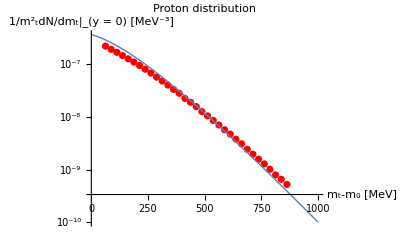

```mathematica
dP=Quiet[Show[ListLogPlot[Protons,PlotStyle->Red,AxesLabel->{"m_t-m_0 [MeV]","1/((m^2)_t)dN/dm_t|_(y = 0) [MeV^-3]",Thick},PlotLabel->"Proton distribution",AxesStyle->Thick],LogPlot[SpB[√((mp+x)^2-mp^2)] 77.6/(77.6+46.5),{x,0,1000},AxesLabel->{"m_t-m_0 [MeV]","1/((m^2)_t)dN/dm_t|_(y = 0) [MeV^-3]",Thick},PlotLabel->"Proton distribution",PlotStyle->Thick,AxesStyle->Thick],PlotRange->All]]
```

```mathematica
(************************************************)
(*       PLOT - rapidity distribution            *)
(************************************************)

(*77.6/(77.6+46.5)Spy[0.0]
77.6/(77.6+46.5)Spy[1.0]*)
```

```mathematica
(************************************************)
(*       Deuteron formation rate                 *)
(************************************************)
A[R1_,R2_]:=3/4(2π)^3 Integrate[(E^(-r^2/4(1/R1^2+1/R2^2)))/(4π  R1 R2)^3 r^2 Sin[θ],{r,0,Infinity},{θ,0,π},Assumptions->{Re[1/R^2+1/Rd^2]>0}]2 Pi 
A[16.02 fm2MeV,Rd=2.12799fm2MeV]

ASPH= 64457.9    (* from the program RAB *)
```

7564.9

64457.9

```mathematica
(************************************************)
(*      D transverse-momentum distribution       *)
(*             A[R,Rd]                           *)
(************************************************)
```

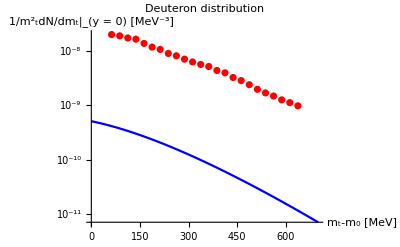

```mathematica
dD=Quiet[Show[LogPlot[A[R,Rd]/(2π) Sp[(√((md+x)^2-md^2))/2]Sn[(√((md+x)^2-md^2))/2],{x,0,700},PlotStyle->Blue,AxesLabel->{"m_t-m_0 [MeV]","1/((m^2)_t)dN/dm_t|_(y = 0) [MeV^-3]",Thick},PlotLabel->"Deuteron distribution",AxesStyle->Thick],ListLogPlot[Deuterons,PlotStyle->Red,AxesLabel->{"m_t-m_0 [MeV]","1/((m^2)_t)dN/dm_t|_(y = 0) [MeV^-3]"},PlotLabel->"Deuteron distribution",PlotStyle->Thick], PlotRange->All]]
```

```mathematica
(************************************************)
(*      D transverse-momentum distribution       *)
(*             ASPH                              *)
(************************************************)
```

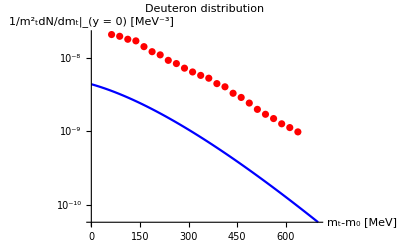

```mathematica
dD=Quiet[Show[LogPlot[ASPH/(2π) Sp[(√((md+x)^2-md^2))/2]Sn[(√((md+x)^2-md^2))/2],{x,0,700},PlotStyle->Blue,AxesLabel->{"m_t-m_0 [MeV]","1/((m^2)_t)dN/dm_t|_(y = 0) [MeV^-3]",Thick},PlotLabel->"Deuteron distribution",AxesStyle->Thick],ListLogPlot[Deuterons,PlotStyle->Red,AxesLabel->{"m_t-m_0 [MeV]","1/((m^2)_t)dN/dm_t|_(y = 0) [MeV^-3]"},PlotLabel->"Deuteron distribution",PlotStyle->Thick], PlotRange->All]]
```

```mathematica
firstbin=ASPH/(2π) Sp[(√((md+x)^2-md^2))/2]Sn[(√((md+x)^2-md^2))/2]/.x->62.5
firstbin/(2*10^-8)
```

3.53769×10^-9

0.176885

```mathematica
Integrate[x^n Exp[-x],{x,0,Infinity},Assumptions->{n>0}]
```

Gamma[1+n]

```mathematica
Gamma[6]
5!
```

120

120

```mathematica
3!!
```

3

```mathematica
√(2/π)2^(z/2)Gamma[z/2+1]/.z->-1
(-1)!!
```

1

1

```mathematica
0!!
```

1

```mathematica
(2.Pi)^3
```

248.05